# 平面における線形変換・アフィン変換

## 0. 図形「お」の定義

```mathematica
Oten:={{3.375,3.375},{3.625,3.625}, {4.625,2.625},{4.375,2.375},{3.375,3.375}};
Oo:={
{0.5,3.375},{0.5,3.625},{1.375,3.625},{1.375,4.5},{1.625,4.5},
{1.625,3.625},{2.5,3.625},{2.5,3.375},{1.625,3.375},{1.625,2},
{3.5,2.625},{4.625,1.5},{3.625,0.375},{3.375,0.625},{4.2,1.5},
{3.4,2.325},{1.625,1.67},{1.625,0.5},{1.375,0.5},{0.5,1.375},
{0.5,1.625},{1.375,1.925},{1.375,3.375},{0.5,3.375}
};
Onaka:={{0.9,1.45},{1.375,1.625},{1.375,1},{0.9,1.45}};
waku:={{0,0},{0,5},{5,5},{5,0},{0,0}}
```

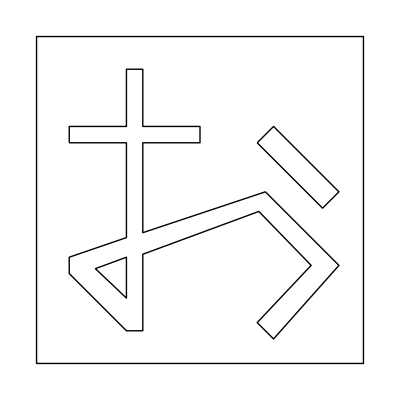

```mathematica
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}]
```

## 1. 回転

```mathematica
R[s_]:=({{Cos[s], -Sin[s]}, {Sin[s], Cos[s]}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[R[s]]],Line[Oo.Transpose[R[s]]],
Line[Onaka.Transpose[R[s]]],Line[waku.Transpose[R[s]]]}
}]
],{s,0,2Pi},SaveDefinitions->True]
```

## 2. 鏡映

```mathematica
S[s_]:=({{Cos[s], Sin[s]}, {Sin[s], -Cos[s]}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[S[s]]],Line[Oo.Transpose[S[s]]],
Line[Onaka.Transpose[S[s]]],Line[waku.Transpose[S[s]]]}
}],
Graphics[{Thick,Red,Line[{10*{Cos[s/2],Sin[s/2]},10*{-Cos[s/2],-Sin[s/2]}}]}]
],{s,0,2Pi},SaveDefinitions->True]
```

## 3. 相似変換

```mathematica
H[a_]:=({{a, 0}, {0, a}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[H[s]]],Line[Oo.Transpose[H[s]]],
Line[Onaka.Transpose[H[s]]],Line[waku.Transpose[H[s]]]}
}]
],{{s,1,"倍率"},-2,2},SaveDefinitions->True]
```

## 4. 横方向の拡大・縮小

```mathematica
Hx[a_]:=({{a, 0}, {0, 1}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[Hx[s]]],Line[Oo.Transpose[Hx[s]]],
Line[Onaka.Transpose[Hx[s]]],Line[waku.Transpose[Hx[s]]]}
}]
],{{s,1,"倍率"},-2,2},SaveDefinitions->True]
```

## 4. 縦方向の拡大・縮小

```mathematica
Hy[a_]:=({{1, 0}, {0, a}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[Hy[s]]],Line[Oo.Transpose[Hy[s]]],
Line[Onaka.Transpose[Hy[s]]],Line[waku.Transpose[Hy[s]]]}
}]
],{{s,1,"倍率"},-2,2},SaveDefinitions->True]
```

## 5. 横方向のせん断

```mathematica
Shx[a_]:=({{1, a}, {0, 1}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[Shx[s]]],Line[Oo.Transpose[Shx[s]]],
Line[Onaka.Transpose[Shx[s]]],Line[waku.Transpose[Shx[s]]]}
}]
],{{s,0,"横ずれの度合い"},-2,1},SaveDefinitions->True]
```

## 6. 縦方向のせん断

```mathematica
Shy[a_]:=({{1, 0}, {a, 1}});
Manipulate[
Show[
Graphics[{Arrow[{{-10,0},{10,0}}],Arrow[{{0,-10},{0,10}}]}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[Shy[s]]],Line[Oo.Transpose[Shy[s]]],
Line[Onaka.Transpose[Shy[s]]],Line[waku.Transpose[Shy[s]]]}
}]
],{{s,0,"縦ずれの度合い"},-2,1},SaveDefinitions->True]
```

## 7. 一般のアフィン変換

```mathematica
A2[a11_,a12_,a21_,a22_]:=({{a11, a12}, {a21, a22}});
Manipulate[
Show[
Graphics[{Arrow[{{-20,0},{20,0}}],Arrow[{{0,-20},{0,20}}]},PlotRange->{{-20,20},{-20,20}}],
Graphics[{Line[Oten],Line[Oo],Line[Onaka],Line[waku]}],
Graphics[{Thick,Blue,
{Line[Oten.Transpose[A2[a11,a12,a21,a22]]+{{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2}}],Line[Oo.Transpose[A2[a11,a12,a21,a22]]+{{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2}}],
Line[Onaka.Transpose[A2[a11,a12,a21,a22]]+{{v1,v2},{v1,v2},{v1,v2},{v1,v2}}],Line[waku.Transpose[A2[a11,a12,a21,a22]]+{{v1,v2},{v1,v2},{v1,v2},{v1,v2},{v1,v2}}]}
}]
],{{a11,1,"表現行列の(1,1)成分"},-2,2},{{a12,0,"表現行列の(1,2)成分"},-2,2},{{a21,0,"表現行列の(2,1)成分"},-2,2},{{a22,1,"表現行列の(2,2)成分"},-2,2},
{{v1,0,"平行移動ベクトルの第1成分"},-5,5},{{v2,0,"平行移動ベクトルの第2成分"},-5,5},SaveDefinitions->True]
```